```mathematica
alphahelper[g_,a_?NumericQ]:=NIntegrate[g[t] Exp[-a t],{t,0,∞}]
findalpha[f_,g_]:=α/.FindRoot[f'[1] alphahelper[g,α]-1,{α,1,0,∞}]
```

```mathematica
findalpha[#1^2&,PDF[GammaDistribution[2,1/2],#]&]
```

0.828427

```mathematica
Integrate[1/(1+x^n),{x,0,∞},Assumptions->{n>1}]
1/%==Sinc[π/n]//FullSimplify
Integrate[Sinc[π/n]/(1+x^n), {x,0,∞},Assumptions->{n>1}]
```

(π Csc[π/n])/n

n Sin[π/n]==π Sinc[π/n]

1

```mathematica
powerdist[n_]:=(Sinc[π/n] UnitStep[#1-1/2])/(1+(#1-1/2)^n)&
```

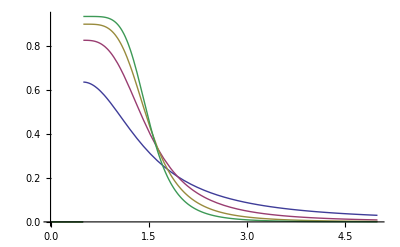

```mathematica
Plot[Table[powerdist[n][x],{n,2,5}]//Evaluate,{x,0,5},PlotRange->All]
```

```mathematica
Table[findalpha[#1^2&,powerdist[n]],{n,2,5}]
```

{0.380625,0.559126,0.626213,0.657832}

```mathematica
powerdist[2]//FullSimplify
```

(Sinc[π/2] UnitStep[#1-1/2])/(1+(#1-1/2)^2)&

```mathematica
powercdf[n_,t_?NumericQ]:=NIntegrate[powerdist[n][y],{y,0,t}]
```

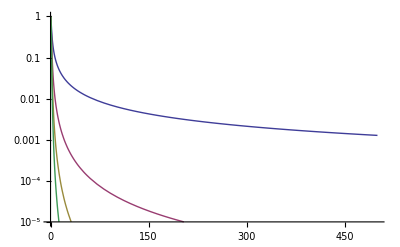

```mathematica
LogPlot[Table[1-powercdf[n,x],{n,2,5}]//Evaluate,{x,0,500},PlotRange->{10^-5,1}]
```

```mathematica
PDF[GammaDistribution[β,1/β],t];
FullSimplify[%,Assumptions->{β>1,t>0}]
```

(ⅇ^(-t β) t^(-1+β) β^β)/Gamma[β]

(ⅇ^(-ⅇ^s β) (ⅇ^s)^β β^β)/Gamma[β]

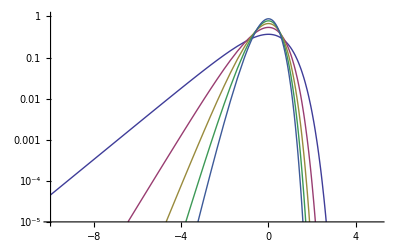

```mathematica
(ⅇ^(-t β) t^(-1+β) β^β)/Gamma[β]*t /.t->Exp[s]
LogPlot[%/.β->{1,2,3,4,5}//Evaluate,{s,-10,5},PlotRange->{10^-5,1}]
```

```mathematica
order[f_]:=Module[{df=D[f[z], z]},Limit[(z df)/f[z],z->0]]
```

(ⅇ^(t (1-k β)) (-1+ⅇ^t)^(-1+(-1+k) β) Gamma[k β])/(Gamma[β] Gamma[(-1+k) β])

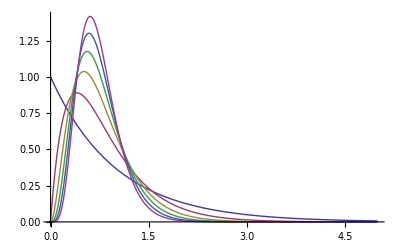

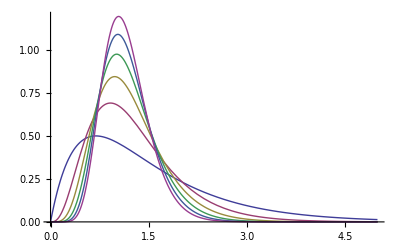

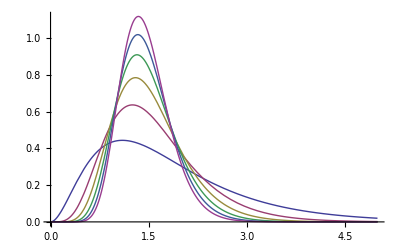

```mathematica
Gamma[k β]/Gamma[β]/Gamma[(k-1)β] Exp[-(k β-1)t](Exp[t]-1)^((k-1)β-1)
Plot[Table[%/.k->2,{β,1,6}]//Evaluate,{t,0,5}]
Plot[Table[%%/.k->3,{β,1,6}]//Evaluate,{t,0,5}]
Plot[Table[%%%/.k->4,{β,1,6}]//Evaluate,{t,0,5}]
Manipulate[Plot[%%%%,{t,0,5},PlotRange->All],{k,2,20,1},{β,1,40}]
```

```mathematica
order[Function[t,Gamma[k β]/Gamma[β]/Gamma[(k-1)β] Exp[-(k β-1)t](Exp[t]-1)^((k-1)β-1)]]
```

-1+(-1+k) β

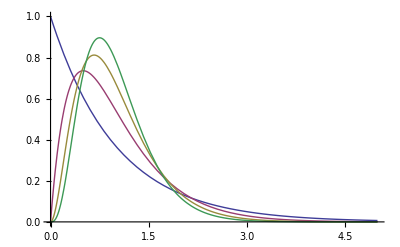

```mathematica
Plot[Table[PDF[GammaDistribution[β,1/β],t],{β,1,4}]//Evaluate,{t,0,5}]
```

```mathematica
Integrate[(ⅇ^(-t β) t^(-1+β) (1/β)^-β)/Gamma[β] Exp[-α t],{t,0,∞}]
```

ConditionalExpression[(1/β)^-β (α+β)^-β,Re[α+β]>0&&Re[β]>0]

```mathematica
Solve[(1/β)^-β (α+β)^-β==1/2,α]
FullSimplify[%,Assumptions->β>1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→-((1/β)^β)^(-1/β) (-2^(1/β)+((1/β)^β)^(1/β) β)}}

{{α→(-1+2^(1/β)) β}}

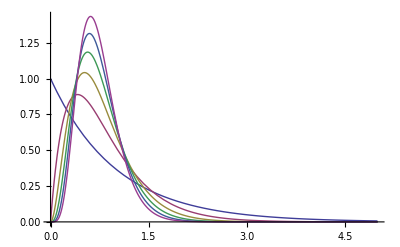

```mathematica
Plot[Table[ PDF[GammaDistribution[β,1/β],t/((-1+2^(1/β)) β)]/((-1+2^(1/β)) β ),{β,1,6}]//Evaluate,{t,0,5}]
```

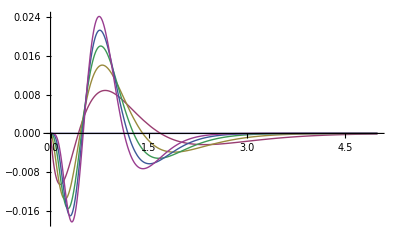

```mathematica
Plot[Table[((-1+2^(1/β))^-β ⅇ^(-t/(-1+2^(1/β))) t^(-1+β))/Gamma[β]-(ⅇ^(t (1-k β)) (-1+ⅇ^t)^(-1+(-1+k) β) Gamma[k β])/(Gamma[β] Gamma[(-1+k) β])/.k->2,{β,1,6}]//Evaluate,{t,0,5},PlotRange->All]
```

```mathematica
Integrate[t (ⅇ^(t (1-k β)) (-1+ⅇ^t)^(-1+(-1+k) β) Gamma[k β])/(Gamma[β] Gamma[(-1+k) β]),{t,0,∞},Assumptions->{k≥2,β≥1}]
```

-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β]

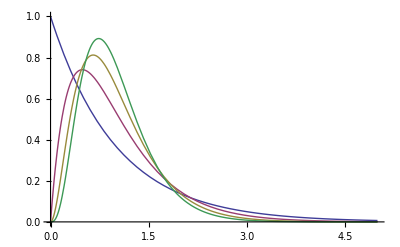

```mathematica
Plot[Table[(ⅇ^(t (1-k β) (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])) (-1+ⅇ^(t (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])))^(-1+(-1+k) β) Gamma[k β] (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β]))/(Gamma[β] Gamma[(-1+k) β])/.k->2,{β,1,4}]//Evaluate,{t,0,5}]
```

```mathematica
(ⅇ^(t (1-k β) (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])) (-1+ⅇ^(t (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])))^(-1+(-1+k) β) Gamma[k β] (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β]))/(Gamma[β] Gamma[(-1+k) β])/.{k->2,β->4}
Series[%,{t,0,3}]
```

319/3 ⅇ^(-319 t/60) (-1+ⅇ^(319 t/420))^3

(10355301121 t^3)/222264000+O[t]^4

```mathematica
norm[n_]:= (-1+2 n) ExpIntegralE[2 n,2 n]
logdist[n_]:=Function[x,Evaluate[1/(x norm[n])(norm[n] 2^(-1+2 n) n^(-1+2 n) (-1+2 n) Log[x norm[n]]^(-2 n)) UnitStep[Exp[-2 n]-x norm[n]]]]
```

```mathematica
Exp[-2*1]/norm[1]//N
```

3.60565

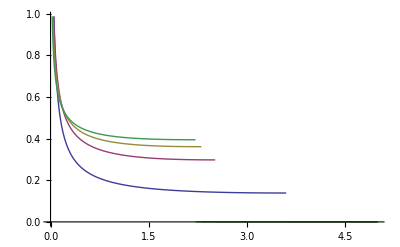

```mathematica
Plot[Table[logdist[n][x],{n,1,4}]//Evaluate,{x,0,5}]
```

```mathematica
hat[p_,w_]:=Module[{z},Sum[SeriesCoefficient[p[z],{z,0,k}] Pochhammer[1+w,k]/Gamma[k+1],{k,0,∞}]]
```

```mathematica
gtilde[f_,P_,w_]:=hat[P,w]/hat[f[#1 P[#1]]/#1&,w]
```

```mathematica
gtildedenom[f_,P_,w_]:=hat[f[#1 P[#1]]/#1&,w]
```

```mathematica
h[p_,W_]:=Module[{z,λ},λ=∑_(k=0)^∞ SeriesCoefficient[p[z],{z,0,k}] (k+1);∑_(k=0)^∞ (SeriesCoefficient[p[z],{z,0,k}] λ^(k+1) W^k Exp[-λ W])/Gamma[k+1]]
```

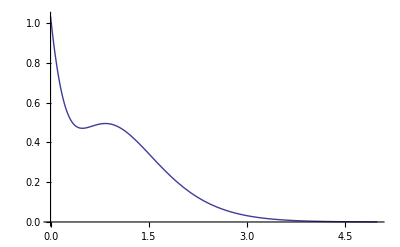

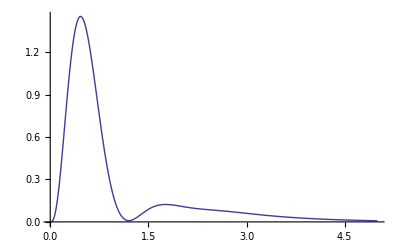

```mathematica
r+(1-r)#^3&/.r->0.35//N;
Plot[h[%,W]//Evaluate,{W,0,5},PlotRange->All]
gtilde[#^2&,%%,w];
InverseLaplaceTransform[%,w,t];
Plot[{%,powerdist[2][x/0.38062542450503556*x]/0.38062542450503556},{t,0,5},PlotRange->All,Exclusions->None]
```

{(2568 w+3214 w^2+1455 w^3+295 w^4+27 w^5+w^6-6 √35 √(11568 w+18364 w^2+11400 w^3+3475 w^4+522 w^5+31 w^6))/(-2892 w+1324 w^2+1245 w^3+295 w^4+27 w^5+w^6),(2568 w+3214 w^2+1455 w^3+295 w^4+27 w^5+w^6+6 √35 √(11568 w+18364 w^2+11400 w^3+3475 w^4+522 w^5+31 w^6))/(-2892 w+1324 w^2+1245 w^3+295 w^4+27 w^5+w^6)}

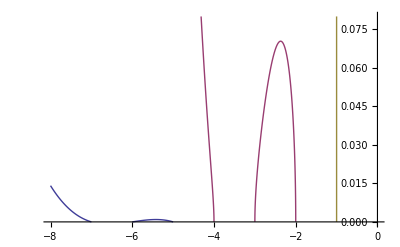

{0.0703632,{w→-2.3695}}

{0.000916444,{w→-5.42251}}

```mathematica
r/.Solve[gtildedenom[#^2&,r+(1-r)#^3&,w]==0,r]
Plot[Join[%,{10^10*(w+1)}]//Evaluate,{w,-8,0},PlotRange->{0,0.08},Exclusions->1,PlotPoints->10000]
FindMaximum[%%[[2]],{w,-3,-2}]
FindMaximum[%%%[[1]],{w,-6,-4}]
```